```mathematica
SetDirectory["~/Documents/GitHub/AvoidedQP/trash_codes/exact_small"]
```

/Users/pwrzosek/Documents/GitHub/AvoidedQP/trash_codes/exact_small

```mathematica
AppendTo[$Path,"~/MathematicaPkg/"];
<<CustomTicks`;
<<MaTeX`;
```

```mathematica
getAssoc[filename_]:=(
result={};
Do[(
file=StringJoin[filename,".json"];
sData=Import[StringJoin["data/", file],"RawJSON"];
result=Join[result,sData];
),{J,JRange}];
result
)
```

```mathematica
getStruct[ds_]:=(
sizeAvail=Normal[DeleteDuplicates[ds[Take,"size"]]];
couplingAvail=Normal[DeleteDuplicates[ds[Take,"coupling"]]];
interactionAvail=Normal[DeleteDuplicates[ds[Take,"interaction"]]];
<|"size"->sizeAvail,"coupling" ->couplingAvail,"interaction"->interactionAvail|>
)
```

```mathematica
extractData[ds_,directive_,keys_]:=(
data=Apply[ds,directive];
{x,y}=Table[(data[Take,keys[[i]]]//Normal)[[1]],{i,1,2}];

Return[Table[{x[[i]],y[[i]]/y[[sizeAvail[[1]]]]},{i,sizeAvail[[1]],Length[x]}]]
)
```

```mathematica
StandardNumberForm[x_]:=If[FractionalPart[x]==0,IntegerPart[x],x];
tlf=(MaTeX[ToString[StandardNumberForm[#]]]&);
```

```mathematica
getDPlot[spc_,n_]:=(
SetOptions[MaTeX,Magnification->2];

fs=22;
tckn=0.005;

plt=ListPlot[spc,
SetOptions[LinTicks,TickLengthScale->1.5];
ImageSize->360,
Joined->False,
PlotMarkers->{Automatic,8},
Frame->True,Axes->False,
FrameStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
LabelStyle->Directive[Black,fs,FontFamily->"CMU Serif"],
PlotRange->{{0,n-1},{0,1}},
PlotRangeClipping->False,
PlotLegends->Placed[StandardNumberForm/@(Normal[spcAvail["interaction"]]),Right],
ClippingStyle->Automatic,
AspectRatio->0.85,
FrameLabel->MaTeX@{"n","c_n / c_0"},
Epilog->{},
FrameTicks->{LinTicks[0,1,0.5,5],LinTicks[0,1,0.5,5,ShowTickLabels->False],LinTicks[-30,30,1,1],LinTicks[-30,30,1,1,ShowTickLabels->False]}
];

plt
)
```

```mathematica
makePlotsSpc[]:=(
dirc={Select[#interaction==KK&]};
keys={"magnons","coefficients"};

plots={};
buff={};
Do[(
spc=extractData[spcDataset,dirc,keys];
AppendTo[buff,spc];
),{KK,spcAvail["interaction"]//Normal}];
AppendTo[plots,getDPlot[buff,Normal[spcAvail["size"]][[1]]]];


plots
)
```

```mathematica
filelist={
"mc_8_h",
"mc_12_h"
};
spcPlots={};
Do[(
spcDataset=Dataset[getAssoc[filename]];
spcAvail=Dataset[getStruct[spcDataset]];
AppendTo[spcPlots,makePlotsSpc[]];
),{filename,filelist}]
```

```mathematica
spcAvail
```

```mathematica
(*SavePlots[]:=(
Do[(
Do[(
Do[(
fileName=StringJoin["plots/",head<>"r","/",
head<>"r","_L=",ToString[spcAvail["size"][[iN]]],
"_J=",ToString[spcAvail["coupling"][[iJ]]],
"_B=",ToString[spcAvail["interaction"][[iB]]],
".jpg"];
Export[fileName,spcPlots[[iN,iJ,iB]],ImageResolution->300];
),{iB,Length[spcAvail["interaction"]//Normal]}]
),{iJ,Length[spcAvail["coupling"]//Normal]}]
),{iN,Length[spcAvail["size"]//Normal]}]
)*)
```

```mathematica
(*SavePlots[]*)
```

```mathematica
(*spcDataset*)
```

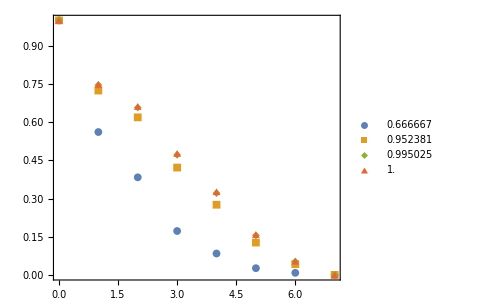
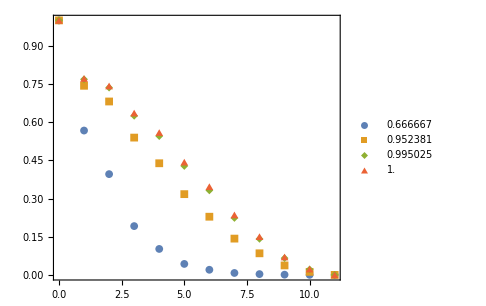

```mathematica
spcPlots//Grid
```

```mathematica
dirc={Select[#interaction==spcAvail["interaction"][[4]]&]};
keys={"magnons","coefficients"};
```

```mathematica
extractData[spcDataset,dirc,keys]
```

{{0,1.},{1,0.771546},{2,0.742388},{3,0.635851},{4,0.55916},{5,0.442955},{6,0.346654},{7,0.235653},{8,0.150285},{9,0.0704037},{10,0.0230546},{11,1.21793×10^-8}}

```mathematica
spcDataset
```